```mathematica
import[file_]:=Module[{imp,toe,data,combined,lasts},
imp=Import["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data/"~~ToString@file];
toe=ToExpression/@StringSplit[imp];
data=Partition[toe,2];
combined=Gather[data,#1[[1]]==#2[[1]]&];
lasts={#[[1,1]],Max@#[[All,2]]}&/@combined;
{StringSplit[file,"-"][[1]],lasts}
]
```

```mathematica
SetDirectory["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data"]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data

```mathematica
data=import/@FileNames["*.txt"]
```

{{cache,{{1,7},{2,10},{3,22},{4,37},{5,213},{6,304},{7,753},{8,1310},{9,2583},{10,5240},{11,7966},{12,22010},{13,37586},{14,62466},{15,121499}}},{cache,{{1,4},{2,7},{3,19},{4,34},{5,274},{6,379},{7,1034},{8,1609},{9,3298},{10,7669},{11,10585},{12,14207},{13,29339},{14,76262},{15,96797},{16,120966}}},{cache,{{1,4},{2,7},{3,19},{4,35},{5,210},{6,301},{7,750},{8,1307},{9,3245},{10,6091},{11,12661},{12,22122},{13,45597},{14,80907},{15,111630},{16,119442}}},{cache,{{1,6},{2,9},{3,21},{4,37},{5,213},{6,304},{7,760},{8,1132},{9,3205},{10,4719},{11,10873},{12,22756},{13,32906},{14,40024},{15,70412},{16,111933},{17,119441}}},{irreversible,{{1,7},{2,14},{3,45},{4,88},{5,534},{6,812},{7,1345},{8,2978},{9,6440},{10,12179},{11,26877},{12,103593},{13,122505}}},{irreversible,{{1,7},{2,14},{3,45},{4,87},{5,533},{6,811},{7,1348},{8,2985},{9,7626},{10,16138},{11,54015},{12,105500},{13,114294},{14,122006}}},{irreversible,{{1,7},{2,13},{3,44},{4,87},{5,531},{6,808},{7,1339},{8,2947},{9,4668},{10,12756},{11,28884},{12,41984},{13,119435}}},{irreversible,{{1,7},{2,14},{3,46},{4,89},{5,536},{6,813},{7,1347},{8,2959},{9,4686},{10,12776},{11,27288},{12,58921},{13,109795},{14,119417}}},{naive,{{1,9},{2,16},{3,36},{4,71},{5,286},{6,428},{7,1450},{8,2285},{9,6454},{10,14484},{11,20761},{12,67361},{13,120661}}},{naive,{{1,11},{2,18},{3,38},{4,72},{5,284},{6,426},{7,1641},{8,2635},{9,7391},{10,13674},{11,37895},{12,69599},{13,122837}}},{naive,{{1,8},{2,15},{3,35},{4,69},{5,282},{6,424},{7,1452},{8,3372},{9,9904},{10,14572},{11,50286},{12,75063},{13,119406}}},{naive,{{1,9},{2,15},{3,35},{4,70},{5,284},{6,425},{7,1556},{8,2747},{9,6184},{10,16100},{11,34464},{12,99172},{13,105545},{14,119422}}},{stockfish,{{1,2},{2,2},{3,2},{4,2},{5,4},{6,6},{7,7},{8,9},{9,14},{10,22},{11,35},{12,47},{13,158},{14,280},{15,445},{16,669},{17,1103},{18,1714},{19,2526},{20,2861},{21,3685},{22,6791},{23,12959},{24,15692},{25,20371},{26,29526},{27,38528},{28,48625},{29,75677},{30,120004}}},{stockfish,{{1,1},{2,1},{3,1},{4,2},{5,3},{6,5},{7,7},{8,9},{9,14},{10,21},{11,35},{12,47},{13,158},{14,281},{15,446},{16,672},{17,1108},{18,1720},{19,2535},{20,2870},{21,3698},{22,6813},{23,12996},{24,15738},{25,20433},{26,29614},{27,38641},{28,48766},{29,75889},{30,119988}}},{stockfish,{{1,1},{2,1},{3,1},{4,2},{5,3},{6,5},{7,7},{8,9},{9,14},{10,21},{11,35},{12,47},{13,158},{14,281},{15,446},{16,672},{17,1107},{18,1720},{19,2534},{20,2870},{21,3697},{22,6812},{23,12999},{24,15739},{25,20431},{26,29610},{27,38638},{28,48763},{29,75894},{30,119987}}}}

```mathematica
medians=Gather[data,#1[[1]]==#2[[1]]&]//{#[[1,1]],Sequence@@#&/@#[[All,2,All]]}&/@#&//{#[[1]],{#[[1,1]],Median@#[[All,2]]}&/@Gather[#[[2]],#[[1]]==#2[[1]]&]}&/@#&
```

{{cache,{{1,5},{2,8},{3,20},{4,36},{5,213},{6,304},{7,1513/2},{8,2617/2},{9,3225},{10,11331/2},{11,10729},{12,22066},{13,35246},{14,69364},{15,208427/2},{16,119442},{17,119441}}},{irreversible,{{1,7},{2,14},{3,45},{4,175/2},{5,1067/2},{6,1623/2},{7,1346},{8,5937/2},{9,5563},{10,12766},{11,28086},{12,81257},{13,233729/2},{14,241423/2}}},{naive,{{1,9},{2,31/2},{3,71/2},{4,141/2},{5,284},{6,851/2},{7,1504},{8,2691},{9,13845/2},{10,14528},{11,72359/2},{12,72331},{13,240067/2},{14,119422}}},{stockfish,{{1,1},{2,1},{3,1},{4,2},{5,3},{6,5},{7,7},{8,9},{9,14},{10,21},{11,35},{12,47},{13,158},{14,281},{15,446},{16,672},{17,1107},{18,1720},{19,2534},{20,2870},{21,3697},{22,6812},{23,12996},{24,15738},{25,20431},{26,29610},{27,38638},{28,48763},{29,75889},{30,119988}}}}

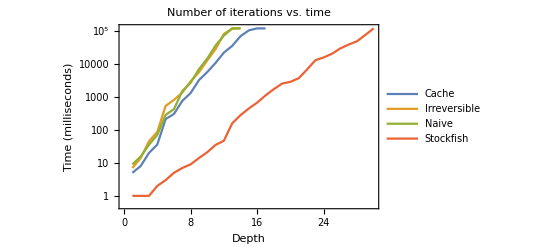

```mathematica
ttdGraph=Module[{d,cache,irreversible,naive,stockfish,legends,labels,lp,joined},
d=medians;
cache=Select[d,#[[1]]=="cache"&][[1,2]];
irreversible=Select[d,#[[1]]=="irreversible"&][[1,2]];
naive=Select[d,#[[1]]=="naive"&][[1,2]];
stockfish=Select[d,#[[1]]=="stockfish"&][[1,2]];

legends={"Cache","Irreversible","Naive","Stockfish"};
labels={"Depth","Time (milliseconds)"};
lp=ListLogPlot[{cache,irreversible,naive,stockfish},PlotLegends->legends,PlotLabel->"Number of iterations vs. time",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[1]];
joined=ListLogPlot[{cache,irreversible,naive,stockfish},PlotLegends->legends,FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[2]];
ListLogPlot[{cache,irreversible,naive,stockfish},PlotLegends->legends,PlotLabel->"Number of iterations vs. time",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True]
]
```

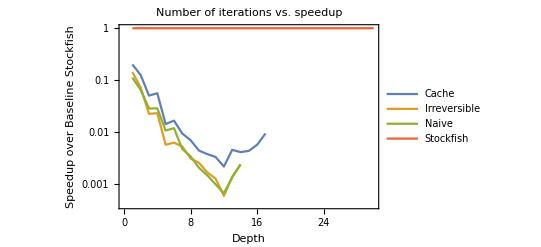

```mathematica
ttdSpeedupGraph=Module[{d,cache,irreversible,naive,stockfish,legends,labels,lp,joined,tS,speedup},
d=medians;
cache=Select[d,#[[1]]=="cache"&][[1,2]];
irreversible=Select[d,#[[1]]=="irreversible"&][[1,2]];
naive=Select[d,#[[1]]=="naive"&][[1,2]];
stockfish=Select[d,#[[1]]=="stockfish"&][[1,2]];
tS=stockfish[[All,2]];
speedup[data_]:=MapThread[{#[[1]],#2/#[[2]]}&,{data,tS[[;;Length@data]]}];

legends={"Cache","Irreversible","Naive","Stockfish"};
labels={"Depth","Speedup over Baseline Stockfish"};
lp=ListLogPlot[speedup/@{cache,irreversible,naive,stockfish},PlotLegends->legends,PlotLabel->"Number of iterations vs. speedup",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[1]];
joined=ListLogPlot[{cache,irreversible,naive,stockfish},PlotLegends->legends,FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[2]];
ListLogPlot[speedup/@{cache,irreversible,naive,stockfish},PlotLegends->legends,PlotLabel->"Number of iterations vs. speedup",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True]
]
```

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/timetodepth.png",ttdGraph]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/timetodepth.png

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/speedup.png",ttdSpeedupGraph]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/speedup.png

```mathematica
?Gather
```

Gather[list] gathers the elements of list into sublists of identical elements.
Gather[list,test] applies test to pairs of elements to determine if they should be considered identical.

```mathematica
importTT=Module[{imp,toe,sp,toexpression,addthreadsmins,parse},
imp=Import["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data/STDOUT4"];
toe=StringSplit[imp,"\n"];
sp=Split[toe,((StringStartsQ[#,"threads"])&&(!StringStartsQ[#2,"threads"]))||((!StringStartsQ[#,"threads"])&&(!StringStartsQ[#2,"threads"]))&];
parse[toprow_]:=ToExpression/@StringSplit[toprow,{" ",","}][[3;;;;4]];
toexpression={parse@#[[1]],Sequence@@ToExpression/@StringSplit/@#[[2;;]]}&/@sp
]
```

{{{2,1,5},{0.0442217,0.155097,0.00371987},{0.0351221,0.115801,0.00225138}},{{2,2,5},{0.0856974,0.275683,0.0641861},{0.0727898,0.230789,0.0169804}},{{2,3,5},{0.138814,0.416875,0.023168},{0.124012,0.377061,0.00991477}},{{2,5,5},{0.185771,0.511808,0.0151138},{0.207104,0.568573,0.0974304}},{{2,10,5},{0.366551,0.8099,0.0301432},{0.388257,0.838312,0.0988458}},{{2,15,5},{0.525639,0.936377,0.0716012},{0.509295,0.922823,0.109242}},{{2,30,5},{0.761178,0.995411,4.31921},{0.777789,0.996823,0.859298}},{{3,1,5},{0.0460015,0.154497,0.0134927},{0.0415699,0.130216,0.00274592},{0.0494611,0.160135,0.0491716}},{{3,2,5},{0.0787202,0.230693,0.0951242},{0.093993,0.282068,0.00688176},{0.0934759,0.287551,0.00814249}},{{3,3,5},{0.114736,0.325863,0.0188472},{0.132243,0.388722,0.00877164},{0.136209,0.389354,0.0216137}},{{3,5,5},{0.175216,0.478605,0.0162773},{0.208383,0.550135,0.01725},{0.206077,0.545473,0.0480273}},{{3,10,5},{0.316474,0.733956,0.130629},{0.362137,0.801777,0.0391178},{0.362943,0.805611,0.0594127}},{{3,15,5},{0.478242,0.898384,0.0403004},{0.479735,0.90427,0.116056},{0.413307,0.840329,0.0341363}},{{3,30,5},{0.747018,0.993855,0.0589786},{0.701205,0.98868,0.0534202},{0.74935,0.994263,0.416865}},{{4,1,5},{0.0474498,0.13998,0.00692438},{0.0584625,0.176527,0.0222845},{0.0498507,0.145984,0.0236022},{0.0581475,0.173547,0.00423199}},{{4,2,5},{0.0936632,0.273206,0.00769257},{0.097808,0.282113,0.00667956},{0.106421,0.312545,0.00833804},{0.104669,0.310542,0.00717367}},{{4,3,5},{0.155136,0.437084,0.0148999},{0.147837,0.412523,0.2199},{0.161317,0.440188,0.0267502},{0.153486,0.408939,0.014189}},{{4,5,5},{0.232323,0.572092,0.0240051},{0.242498,0.601402,0.0875017},{0.244332,0.610606,0.018319},{0.230633,0.580181,0.0206635}},{{4,10,5},{0.439518,0.857903,0.0344986},{0.444205,0.861801,0.137394},{0.425122,0.848096,0.0386488},{0.421776,0.846307,0.139839}},{{4,15,5},{0.559192,0.946843,0.0475781},{0.557539,0.948104,0.2851},{0.573836,0.95376,0.25883},{0.572823,0.952892,0.0719267}},{{4,30,5},{0.791976,0.997003,0.0515004},{0.805633,0.997731,0.083069},{0.803677,0.997771,0.0660852},{0.789837,0.997159,0.0767522}},{{6,1,5},{0.0554877,0.160777,0.0123303},{0.0563282,0.162286,0.0250105},{0.0480865,0.138244,0.00922134},{0.0491292,0.140935,0.00543762},{0.0557005,0.160438,0.00874084},{0.047578,0.138607,0.00969012}},{{6,2,5},{0.107748,0.280947,0.00806741},{0.107987,0.28844,0.0930625},{0.113186,0.305696,0.017556},{0.111756,0.299762,0.0390701},{0.114005,0.308863,0.0448912},{0.10583,0.283195,0.0128246}},{{6,3,5}}}